Aufgabe 2.1

{0.471238+4.48793 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.471238 | 0.246798 | 1.90941 | 0.0785266
x | 4.48793 | 0.0271442 | 165.337 | 5.46009×10^-23}

Aufgabe 3.1, Spaltbreite

{-2.72955+5.55455 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | -2.72955 | 0.465354 | -5.86552 | 0.000158252
x | 5.55455 | 0.0632292 | 87.8478 | 8.93749×10^-16}

Aufgabe 3.1, Spaltabstand

{0.281818+6.97273 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.281818 | 0.254553 | 1.10711 | 0.296957
x | 6.97273 | 0.0375317 | 185.782 | 1.92918×10^-17}

Aufgabe 3.3

{-0.139583+11.7648 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | -0.139583 | 0.297421 | -0.469313 | 0.653113
x | 11.7648 | 0.052853 | 222.594 | 9.74978×10^-15}

Aufgabe 2.4

{6.4+18.2 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 6.4 | 3.00333 | 2.13097 | 0.122899
x | 18.2 | 0.905539 | 20.0985 | 0.000269228}

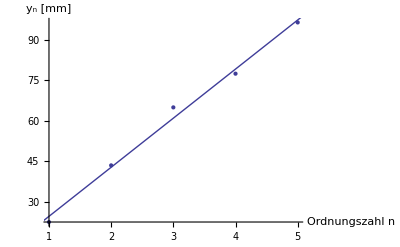

```mathematica
Needs["ErrorBarPlots`"]
werte21:= {{4.5, 4.5,5,4.75,5.25},{9.5,10,9,7,9.75},{14,14,13.5,14,14},{18,18.5,18.25,18.5,18.75},{24,22.75,22.75,22.75,23},{27,27.5,27.5,27.5,27.75},{34,32,31.5,32,31.5},{36.5,36.5,36.75,35.5,36.25},{42.5,41,41.5,40.25,41},{47.25,45.5,45.75,45.5,44.25},{51.5,49.5,50.25,48.5,49},{57,54.25,55.25,53.5,54},{61.5,58.5,59.25,58,58.5},{56.6,63.5,63.5,62.75,63.5},{69.75,67.5,67.75,67,67.5}};
werte31a:={{2.5,3,2.75,5,5.5},{7,7.5,7.75,10,10.5},{12.75,12.5,13.5,16,15.5},{18.75,18.5,19,21,22},{23.75,23.5,23.5,26,27},{28.5,28.5,28.5,31,32},{33.75,34.5,33.5,37.5,37.5},{39.5,39.5,39.5,42,43.5},{46.75,45,45,47.5,49},{55,48.5,52,52.5,56},{64.5,54.5,58,58,62.5},{66.75,61,63,64,69}};
werte31b:={{7,7.5,7,9.5,8},{13.5,14,11.5,14,14},{20.5,24,20,20.5,20.5},{29,30.5,27,27.5,27.5},{37,36.5,33.5,33,37.5},{41,41,43.5,40,44.5},{47.5,51,48,48,51},{55,58.5,54.5,54.5,57},{62.5,65.5,61,61.5,66.5},{69.5,71.5,68,69,72.5},{75,79,75,76,78.5}};
werte33:={{12,12,11.5,12,11},{24,23,22.75,23.5,23},{34.5,35.25,35.25,35.35},{47.25,47.5,47,47,46.75},{58.75,58.5,58.25,59,58.5},{70.5,70.5,69.25,70.5,70},{82.25,87.25,81,82.25,82.5} ,{93.5,93.35,93.75,93.5,93},{106.5,105.5,105.25,105.75,106}};

plotErrorBars[list_]:=Module[{result={}},
For[i=1,i≤Length[list],i++,
AppendTo[result,
{i, Mean[list[[i]]] ,StandardDeviation[list[[i]]]}
];
];
result
]
modelFitPoints[list_]:=Module[{result={}},
For[i=1,i≤Length[list],i++,
AppendTo[result,{i,Mean[list[[i]]]}]
];
result
]

plotStuff[werte_,text_]:=Module[{},
errorBars=plotErrorBars[werte];
fitPoints=modelFitPoints[werte];
model=LinearModelFit[fitPoints,x,x];

gm=Plot[model["BestFit"],{x,0,16},PlotStyle->{Red}];
ge=ErrorListPlot[errorBars,Frame->{Left,Bottom},FrameLabel->{Style["Ordnungszahl n",12,FontFamily->"Arial"],Style[Row[{Subscript[y,n] ," [mm]"}],12,FontFamily->"Arial"]}];
(*Show[ge, gm]*)
Print[text];
model[{"BestFit","ParameterTable"}]
(*errorBars*)
]

plotStuff[werte21, "Aufgabe 2.1"]
plotStuff[werte31a, "Aufgabe 3.1, Spaltbreite"]
plotStuff[werte31b, "Aufgabe 3.1, Spaltabstand"]
plotStuff[werte33, "Aufgabe 3.3"]

(* Aufgabe 2.4 *)
werte24:={{1,22.5},{2,43.5},{3,65},{4, 77.5},{5,96.5}};
model24=LinearModelFit[werte24,x,x];

Print["Aufgabe 2.4"];
model24[{"BestFit","ParameterTable"}]
Show[ListPlot[werte24],Plot[model24["BestFit"],{x,0,6}],AxesLabel->{Style["Ordnungszahl n",12,FontFamily->"Arial"],Style[Row[{Subscript[y,n] ," [mm]"}],12,FontFamily->"Arial"]}]
```